# Some connectivity based cluster validity indices

## 準備

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
(*SetDirectory["/Users/kouamano/gitsrc/ClusteringAdequation/test-data"]*)
```

```mathematica
SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation/test-data"]
```

/Users/amanokou/gitsrc/ClusteringAdequation/test-data

## 基本Programまとめ

minindexをつくる。
Input: dShortMat, Clusteringの結果(クラスタIDのリストのリスト).
output: メンバーID.

最終的に、z[k] = x[k,minindex]; z: medoid of cluster k, x: minindex-th member of cluster k、を求める。

距離行列から特定のクラスタに関する部分距離行列を抜き出す。

```mathematica
subDMat[dmat_,members_]:=Transpose[Transpose[dmat[[members]]][[members]]]
```

部分距離行列をもとに特定のクラスタのargminを求める。

```mathematica
argMinDMat[dMat_]:=Module[{sumList},
sumList=Map[Tr[#]&,dMat];
Position[sumList,Min[sumList]][[1]]
]
```

距離行列とクラスタリング結果から各クラスタのmedoidをもとめる。

```mathematica
findMedoidsParCL[dmat_,clusterResult_]:=Map[argMinDMat[subDMat[dmat,#]]&,clusterResult]
```

各クラスタのmedoid番号からもとのサンプル番号を求める。

```mathematica
orgIndexFromMedoidParCL[medoids_,clusterResult_]:=Inner[Part,clusterResult,medoids,List]
```

## Sample

```mathematica
sample={{1,1,2},
{2,1,4},
{3,3,5},
{4,5,4},
{3,2,5},
{1,3,1}
}
```

{{1,1,2},{2,1,4},{3,3,5},{4,5,4},{3,2,5},{1,3,1}}

## FindClusters Examples

```mathematica
fc=FindClusters[sample->Range[Length[sample]],3,Method->"Agglomerate"]
```

{{1,6},{2,3,5},{4}}

## DistanceMatrix

```mathematica
sampleDmat=Outer[EuclideanDistance,sample//N,sample,1]
```

{{0.,2.23607,4.12311,5.38516,3.74166,2.23607},{2.23607,0.,2.44949,4.47214,1.73205,3.74166},{4.12311,2.44949,0.,2.44949,1.,4.47214},{5.38516,4.47214,2.44949,0.,3.31662,4.69042},{3.74166,1.73205,1.,3.31662,0.,4.58258},{2.23607,3.74166,4.47214,4.69042,4.58258,0.}}

```mathematica
Export["sample.dmat",sampleDmat,"TSV"]
```

sample.dmat

RNG_d df = sample.dmat size = 6 > sample.RNGd

mk_d _short _mat loop = 6 dsize = 6 ef = sample.RNGd > sample.dsmat

```mathematica
sampleDSmat=Import["sample.dsmat","Table"]
```

{{2.23607,2.23607,2.23607,2.44949,2.23607,2.23607},{2.23607,1.73205,1.73205,2.44949,1.73205,2.23607},{2.23607,1.73205,1.,2.44949,1.,2.23607},{2.44949,2.44949,2.44949,2.44949,2.44949,2.44949},{2.23607,1.73205,1.,2.44949,1.,2.23607},{2.23607,2.23607,2.23607,2.44949,2.23607,2.23607}}

```mathematica
sampleDSmatZeroself=ReplacePart[sampleDSmat,{x_,x_}->0]
```

{{0,2.23607,2.23607,2.44949,2.23607,2.23607},{2.23607,0,1.73205,2.44949,1.73205,2.23607},{2.23607,1.73205,0,2.44949,1.,2.23607},{2.44949,2.44949,2.44949,0,2.44949,2.44949},{2.23607,1.73205,1.,2.44949,0,2.23607},{2.23607,2.23607,2.23607,2.44949,2.23607,0}}

```mathematica
subDMat[sampleDmat,fc[[2]]]
```

{{0.,2.44949,1.73205},{2.44949,0.,1.},{1.73205,1.,0.}}

```mathematica
argMinDMat[subDMat[sampleDmat,fc[[2]]]]
```

{3}

```mathematica
medoidsID=findMedoidsParCL[sampleDmat,fc]
```

{{1},{3},{1}}

```mathematica
sampleMedoids=orgIndexFromMedoidParCL[medoidsID,fc]//Flatten
```

{1,5,4}

## cDB

cDB = Sum(R[i],{i,1,K}) / K   ; K:クラスタ数
R[i] = Max[{j,j≠i}]((S[i]+S[j])/d[i,j])   ; i:クラスタi, d[i,j]: ユークリッド距離行列
S[i] = Sum(dshort(x,z[i]),{x,x∈C[i]}) / n[i]   ; z[i]:medoid of cluster i, n[i]:number of cluster points.

### Program

```mathematica
s[dshortMatZeroself_,clMembers_,medoidIndex_]:=Tr[dshortMatZeroself[[medoidIndex,clMembers]]]/Length[clMembers]
```

```mathematica
r[edMat_,dshortMatZeroself_,cls_,medoids_,i_]:=Module[{js},
js=Drop[Range[Length[cls]],{i}];
Max[  Map[(s[dshortMatZeroself,cls[[i]],medoids[[i]]]+s[dshortMatZeroself,cls[[#]],medoids[[#]]])/edMat[[i,#]]&,js]  
]
]
```

```mathematica
cDB[edMat_,dshortMatZeroself_,cls_,medoids_]:=Tr[Table[r[edMat,dshortMatZeroself,cls,medoids,i],{i,Length[cls]}]]
```

### Examples

```mathematica
cDB[sampleDmat,sampleDSmatZeroself,fc,sampleMedoids]
```

2.18633

```mathematica
r[sampleDmat,sampleDSmatZeroself,fc,sampleMedoids,2]
```

0.90727

```mathematica
sampleDSmat[[1]]
```

{2.23607,2.23607,2.23607,2.44949,2.23607,2.23607}

```mathematica
sampleDSmat[[1,{1,4,6}]]
```

{2.23607,2.44949,2.23607}

s : i = 2

```mathematica
s[sampleDSmatZeroself,fc[[1]],sampleMedoids[[1]]]
```

1.11803

```mathematica
s[sampleDSmatZeroself,fc[[2]],sampleMedoids[[2]]]
```

0.910684

```mathematica
s[sampleDSmatZeroself,fc[[3]],sampleMedoids[[3]]]
```

0

## cDunn

cDunn = Min[i, 1, K] (Min[j,1,K ; j≠i]( d(C[i],C[j])/Max[k,1,K](delta(C[k])) ))
delta(C) = Max[x,y ∈ C](dshort(x,y)) ; diameter
d(C[i],C[j]) = Min[x∈C[i] , y∈C[j]](dshort(x,y))
C : クラスタ、K : クラスタ数

### Program

```mathematica
d[cl1_,cl2_,dshortMatZeroself_]:=Module[
{outer},
outer=Flatten[Outer[List,cl1,cl2,1],1];
Min[Map[dshortMatZeroself[[#[[1]],#[[2]]]]&,outer]]
]
```

```mathematica
delta[cl_,dshortMatZeroself_]:=Module[
{subset},
subset=Subsets[cl,{2}];
If[Length[subset]==0,0,Max[Map[dshortMatZeroself[[#[[1]],#[[2]]]]&,subset]]]
]
```

```mathematica
cDunn[cls_,dshortMatZeroself_]:=Module[
{numCls,maxdelta,subset},
numCls=Length[cls];
maxdelta=Max[Map[delta[#,dshortMatZeroself]&,cls]];
subset=Subsets[cls,{2}];
Min[Map[d[#[[1]],#[[2]],dshortMatZeroself]&,subset]]/maxdelta
]
```

### Examples

```mathematica
cDunn[fc,sampleDSmatZeroself]
```

1.

```mathematica
delta[fc[[3]],sampleDSmatZeroself]
```

0

```mathematica
delta2[fc[[2]],sampleDSmatZeroself]
```

0

```mathematica
fc[[2]]
```

{2,3,5}

```mathematica
sampleDSmatZeroself
```

{{0,2.23607,2.23607,2.44949,2.23607,2.23607},{2.23607,0,1.73205,2.44949,1.73205,2.23607},{2.23607,1.73205,0,2.44949,1.,2.23607},{2.44949,2.44949,2.44949,0,2.44949,2.44949},{2.23607,1.73205,1.,2.44949,0,2.23607},{2.23607,2.23607,2.23607,2.44949,2.23607,0}}

```mathematica
d[fc[[2]],fc[[3]],sampleDSmatZeroself]
```

2.44949

```mathematica
fc[[1]]
```

{1,6}

```mathematica
fc[[2]]
```

{2,3,5}

## cPS

cPS=1/K∑_(i=1)^K 1/n[i]∑_(x∈S[i]) (dshort(x,z[i]))/dmin

## test

### cDunn

```mathematica
dsh={
{0,1,2,4,7},
{1,0,3,5,8},
{2,3,0,6,9},
{4,5,6,0,10},
{7,8,9,10,0}
}
```

{{0,1,2,4,7},{1,0,3,5,8},{2,3,0,6,9},{4,5,6,0,10},{7,8,9,10,0}}

```mathematica
cDunn[{{1,2},{3,4,5}},dsh]
```

1/5

### 4_2

```mathematica
sphcsv=Import["/Users/amanokou/sph.csv","Table"];
```

```mathematica
sphcsvDrop=Transpose[Drop[Transpose[sphcsv],-1]];
```

```mathematica
sphdmat=Outer[EuclideanDistance,sphcsvDrop,sphcsvDrop,1];
```

```mathematica
Export["sph.dmat",sphdmat,"Table"]
```

sph.dmat

```mathematica
Export["sphDrop.tsv",sphcsvDrop,Delimiters->" "]
```

sphDrop.tsv

```mathematica
sphcsvG=Gather[sphcsv,#1[[4]]==#2[[4]]&];
```

```mathematica
sphCl={Range[1,100],Range[101,200],Range[201,300],Range[301,400]}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200},{201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300},{301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400}}

```mathematica
sphDshort=Import["tmp","Table"]
```

{{0.351852,0.588303,0.588303,0.660303,0.65,0.65,0.588303,«386»,4.48032,4.48032,4.48032,4.48032,4.48032,4.48032,4.48032},«399»}

```mathematica
sphDshortZeroself=ReplacePart[sphDshort,{x_,x_}->0]
```

{{0,0.588303,0.588303,0.660303,0.65,0.65,0.588303,«386»,4.48032,4.48032,4.48032,4.48032,4.48032,4.48032,4.48032},«399»}

```mathematica
Tr[sphDshortZeroself,List]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
sphDshort
```

{400,400}

```mathematica
cDunn[sphCl,sphDshortZeroself]
```

17.5245

```mathematica
cDB[sphCl,sphDshortZeroself]
```

### 5_2

```mathematica
saha[5,2]=Import["/Users/amanokou/gitsrc/ClusteringAdequation/test-data/5_2.tbl","Table"];
```

```mathematica
saha[5,2]
```

{{11.11,10.14,1},{8.68,9.76,1},{10.04,10.63,1},{8.79,10.13,1},{10.53,8.95,1},{10.58,9.72,1},{11.19,11.6,1},{8.14,10.21,1},{9.62,10.83,1},{11.31,9.7,1},{9.95,8.16,1},{9.84,10.93,1},{10.05,10.35,1},{9.41,11.39,1},{10.91,11.33,1},{10.13,11.76,1},{8.51,11.3,1},{10.2,10.89,1},{9.94,10.1,1},{8.25,9.49,1},{8.93,10.87,1},{8.16,10.69,1},{10.74,8.36,1},{11.79,9.77,1},{9.33,10.64,1},{10.86,11.3,1},{9.04,11.66,1},{8.19,9.17,1},{9.06,10.1,1},{11.49,10.43,1},{9.03,10.04,1},{10.84,10.82,1},{11.09,10.28,1},{11.11,10.39,1},{9.77,8.33,1},{8.24,10.66,1},{9.88,9.48,1},{8.87,10.72,1},{11.42,9.34,1},{9.2,8.49,1},{9.46,9.88,1},{10.86,11.78,1},{9.88,10.23,1},{10.37,9.72,1},{9.26,8.63,1},{11.42,9.06,1},{8.96,10.78,1},{10.38,8.92,1},{8.78,9.96,1},{11.19,10.71,1},{11.81,6.15,2},{10.4,6.66,2},{9.15,5.55,2},{11.43,7.07,2},{8.61,6.62,2},{10.6,7.27,2},{9.49,5.97,2},{10.99,5.51,2},{8.45,6.57,2},{10.69,7.42,2},{10.14,4.86,2},{11.52,7.39,2},{10.04,6.87,2},{11.7,5.99,2},{10.26,6.71,2},{10.06,5.87,2},{10.62,4.81,2},{11.25,7.51,2},{8.17,5.62,2},{8.83,7.48,2},{10.15,6.99,2},{8.76,7.,2},{10.27,7.4,2},{10.91,5.35,2},{9.87,5.55,2},{11.48,5.,2},{10.05,7.96,2},{10.73,6.3,2},{11.89,5.97,2},{9.03,6.44,2},{10.27,7.35,2},{8.86,4.74,2},{9.23,5.94,2},{11.24,6.37,2},{10.22,5.51,2},{8.68,7.15,2},{8.48,5.08,2},{9.97,4.86,2},{8.79,6.09,2},{10.8,7.26,2},{9.87,5.59,2},{9.62,5.06,2},{8.63,7.52,2},{9.24,7.04,2},{8.88,7.35,2},{10.91,7.76,2},{9.87,7.84,2},{9.16,6.18,2},{9.25,4.29,2},{11.37,5.5,2},{13.74,11.7,3},{14.63,11.17,3},{15.44,10.46,3},{13.28,11.27,3},{13.15,10.56,3},{13.16,10.65,3},{13.23,8.76,3},{14.46,8.7,3},{13.21,10.44,3},{13.45,10.2,3},{12.34,10.33,3},{14.32,9.79,3},{15.39,9.18,3},{13.44,9.48,3},{15.09,10.79,3},{12.85,9.3,3},{14.13,8.91,3},{13.19,9.97,3},{13.8,8.84,3},{14.08,10.93,3},{14.53,11.83,3},{13.61,10.37,3},{15.69,9.18,3},{13.95,9.73,3},{13.99,9.22,3},{15.71,9.4,3},{13.77,10.07,3},{14.85,9.43,3},{12.09,10.71,3},{15.88,10.25,3},{13.28,11.25,3},{13.1,11.83,3},{15.65,10.86,3},{12.94,11.38,3},{13.59,10.51,3},{14.52,10.94,3},{13.88,10.65,3},{14.88,10.75,3},{15.73,9.8,3},{12.27,9.45,3},{13.37,10.67,3},{13.51,10.42,3},{13.74,11.9,3},{14.68,10.91,3},{12.56,9.02,3},{13.09,8.48,3},{15.18,9.13,3},{15.31,9.71,3},{13.01,8.33,3},{14.64,8.21,3},{11.12,13.31,4},{11.43,13.45,4},{11.2,15.49,4},{10.93,13.91,4},{11.19,13.24,4},{10.67,14.77,4},{9.94,12.17,4},{9.46,12.35,4},{9.31,15.25,4},{10.31,15.26,4},{10.58,15.4,4},{11.53,12.71,4},{10.88,13.61,4},{9.08,12.46,4},{9.64,12.05,4},{10.42,15.57,4},{11.09,15.2,4},{9.56,13.41,4},{10.94,15.5,4},{9.9,15.62,4},{10.09,15.15,4},{9.39,15.76,4},{10.2,12.66,4},{10.44,13.58,4},{9.08,13.97,4},{9.56,12.32,4},{11.58,14.9,4},{9.17,15.25,4},{11.69,14.05,4},{9.24,13.7,4},{11.67,14.36,4},{10.58,14.32,4},{10.56,14.87,4},{9.47,15.62,4},{8.32,13.62,4},{10.03,15.79,4},{9.41,13.6,4},{11.67,13.58,4},{9.29,12.55,4},{9.93,12.91,4},{10.88,12.93,4},{9.73,14.31,4},{9.92,12.07,4},{8.84,13.29,4},{11.48,14.49,4},{10.65,13.06,4},{11.53,14.4,4},{11.23,12.72,4},{8.89,12.49,4},{9.16,14.12,4},{7.21,9.66,5},{4.79,10.99,5},{5.38,8.74,5},{7.96,9.76,5},{7.1,11.72,5},{5.49,11.63,5},{6.82,11.73,5},{7.26,9.27,5},{5.69,8.95,5},{4.47,9.53,5},{5.06,8.59,5},{5.52,11.29,5},{4.69,9.5,5},{6.02,9.05,5},{4.36,10.93,5},{6.96,9.41,5},{6.61,9.98,5},{7.27,9.04,5},{6.17,11.69,5},{6.14,8.38,5},{6.61,9.06,5},{4.98,8.77,5},{5.03,9.42,5},{4.65,9.12,5},{5.08,9.74,5},{4.95,8.49,5},{7.48,10.64,5},{6.54,10.76,5},{5.6,9.53,5},{6.78,8.98,5},{5.11,8.75,5},{4.6,9.7,5},{4.82,9.54,5},{4.8,10.34,5},{5.54,9.4,5},{5.26,10.29,5},{5.48,10.88,5},{6.92,10.55,5},{6.55,10.25,5},{5.41,10.15,5},{4.45,10.14,5},{5.,8.43,5},{6.62,8.4,5},{7.7,11.15,5},{5.45,9.99,5},{7.01,9.11,5},{6.95,10.75,5},{6.7,9.87,5},{5.71,8.26,5},{5.79,10.67,5}}

```mathematica
sahaDrop[5,2]=Transpose[Drop[Transpose[saha[5,2]],-1]]
```

{{11.11,10.14},{8.68,9.76},{10.04,10.63},{8.79,10.13},{10.53,8.95},{10.58,9.72},{11.19,11.6},{8.14,10.21},{9.62,10.83},{11.31,9.7},{9.95,8.16},{9.84,10.93},{10.05,10.35},{9.41,11.39},{10.91,11.33},{10.13,11.76},{8.51,11.3},{10.2,10.89},{9.94,10.1},{8.25,9.49},{8.93,10.87},{8.16,10.69},{10.74,8.36},{11.79,9.77},{9.33,10.64},{10.86,11.3},{9.04,11.66},{8.19,9.17},{9.06,10.1},{11.49,10.43},{9.03,10.04},{10.84,10.82},{11.09,10.28},{11.11,10.39},{9.77,8.33},{8.24,10.66},{9.88,9.48},{8.87,10.72},{11.42,9.34},{9.2,8.49},{9.46,9.88},{10.86,11.78},{9.88,10.23},{10.37,9.72},{9.26,8.63},{11.42,9.06},{8.96,10.78},{10.38,8.92},{8.78,9.96},{11.19,10.71},{11.81,6.15},{10.4,6.66},{9.15,5.55},{11.43,7.07},{8.61,6.62},{10.6,7.27},{9.49,5.97},{10.99,5.51},{8.45,6.57},{10.69,7.42},{10.14,4.86},{11.52,7.39},{10.04,6.87},{11.7,5.99},{10.26,6.71},{10.06,5.87},{10.62,4.81},{11.25,7.51},{8.17,5.62},{8.83,7.48},{10.15,6.99},{8.76,7.},{10.27,7.4},{10.91,5.35},{9.87,5.55},{11.48,5.},{10.05,7.96},{10.73,6.3},{11.89,5.97},{9.03,6.44},{10.27,7.35},{8.86,4.74},{9.23,5.94},{11.24,6.37},{10.22,5.51},{8.68,7.15},{8.48,5.08},{9.97,4.86},{8.79,6.09},{10.8,7.26},{9.87,5.59},{9.62,5.06},{8.63,7.52},{9.24,7.04},{8.88,7.35},{10.91,7.76},{9.87,7.84},{9.16,6.18},{9.25,4.29},{11.37,5.5},{13.74,11.7},{14.63,11.17},{15.44,10.46},{13.28,11.27},{13.15,10.56},{13.16,10.65},{13.23,8.76},{14.46,8.7},{13.21,10.44},{13.45,10.2},{12.34,10.33},{14.32,9.79},{15.39,9.18},{13.44,9.48},{15.09,10.79},{12.85,9.3},{14.13,8.91},{13.19,9.97},{13.8,8.84},{14.08,10.93},{14.53,11.83},{13.61,10.37},{15.69,9.18},{13.95,9.73},{13.99,9.22},{15.71,9.4},{13.77,10.07},{14.85,9.43},{12.09,10.71},{15.88,10.25},{13.28,11.25},{13.1,11.83},{15.65,10.86},{12.94,11.38},{13.59,10.51},{14.52,10.94},{13.88,10.65},{14.88,10.75},{15.73,9.8},{12.27,9.45},{13.37,10.67},{13.51,10.42},{13.74,11.9},{14.68,10.91},{12.56,9.02},{13.09,8.48},{15.18,9.13},{15.31,9.71},{13.01,8.33},{14.64,8.21},{11.12,13.31},{11.43,13.45},{11.2,15.49},{10.93,13.91},{11.19,13.24},{10.67,14.77},{9.94,12.17},{9.46,12.35},{9.31,15.25},{10.31,15.26},{10.58,15.4},{11.53,12.71},{10.88,13.61},{9.08,12.46},{9.64,12.05},{10.42,15.57},{11.09,15.2},{9.56,13.41},{10.94,15.5},{9.9,15.62},{10.09,15.15},{9.39,15.76},{10.2,12.66},{10.44,13.58},{9.08,13.97},{9.56,12.32},{11.58,14.9},{9.17,15.25},{11.69,14.05},{9.24,13.7},{11.67,14.36},{10.58,14.32},{10.56,14.87},{9.47,15.62},{8.32,13.62},{10.03,15.79},{9.41,13.6},{11.67,13.58},{9.29,12.55},{9.93,12.91},{10.88,12.93},{9.73,14.31},{9.92,12.07},{8.84,13.29},{11.48,14.49},{10.65,13.06},{11.53,14.4},{11.23,12.72},{8.89,12.49},{9.16,14.12},{7.21,9.66},{4.79,10.99},{5.38,8.74},{7.96,9.76},{7.1,11.72},{5.49,11.63},{6.82,11.73},{7.26,9.27},{5.69,8.95},{4.47,9.53},{5.06,8.59},{5.52,11.29},{4.69,9.5},{6.02,9.05},{4.36,10.93},{6.96,9.41},{6.61,9.98},{7.27,9.04},{6.17,11.69},{6.14,8.38},{6.61,9.06},{4.98,8.77},{5.03,9.42},{4.65,9.12},{5.08,9.74},{4.95,8.49},{7.48,10.64},{6.54,10.76},{5.6,9.53},{6.78,8.98},{5.11,8.75},{4.6,9.7},{4.82,9.54},{4.8,10.34},{5.54,9.4},{5.26,10.29},{5.48,10.88},{6.92,10.55},{6.55,10.25},{5.41,10.15},{4.45,10.14},{5.,8.43},{6.62,8.4},{7.7,11.15},{5.45,9.99},{7.01,9.11},{6.95,10.75},{6.7,9.87},{5.71,8.26},{5.79,10.67}}

```mathematica
(sahaEDist[5,2]=Outer[EuclideanDistance,saha[5,2],saha[5,2],1])//Dimensions
```

{250,250}

```mathematica
Export["saha_5_2.dmat",sahaEDist[5,2],"Table"]
```

saha_5_2.dmat

```mathematica
sahaDShort[5,2]=Import["tmp3","Table"]
```

{{0.141421,0.643817,0.643817,0.643817,0.750733,0.643817,0.480416,«237»,2.05896,2.05896,2.05896,2.05896,2.05896,2.05896},«249»}

```mathematica
sahaDShortZeroself[5,2]=ReplacePart[sahaDShort[5,2],{x_,x_}->0]
```

{{0,0.643817,0.643817,0.643817,0.750733,0.643817,0.480416,«236»,2.05896,2.05896,2.05896,2.05896,2.05896,2.05896,2.05896},«249»}

```mathematica
Map[#[[3]]&,saha[5,2]];
```

```mathematica
sahaCls[5,2]={Range[1,50],Range[51,100],Range[101,150],Range[151,200],Range[201,250]};
```

```mathematica
cDunn[sahaCls[5,2],sahaDShortZeroself[5,2]]
```

10.351

```mathematica
cDunn[sahaCls[5,2],sahaDShort[5,2]]
```

10.351

```mathematica
cDunn2[sahaCls[5,2],sahaDShort[5,2]]
```

0.00409878

階層クラスタリング

```mathematica
clAg=Agglomerate[sahaDrop[5,2]->Range[250],DistanceFunction->EuclideanDistance,Linkage->"Single"];
```

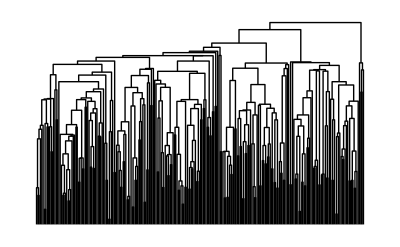

```mathematica
DendrogramPlot[clAg]
```

```mathematica
Map[ClusterFlatten[#]&,ClusterSplit[clAg,5]]
```

{{1,33,34,50,32,30,26,15,7,42,10,39,46,24,140,145,116,114,118,110,142,122,135,141,106,105,109,137,127,120,124,112,136,144,102,138,115,103,133,130,139,126,123,113,147,148,128,125,117,119,108,150,107,146,149,131,104,134,132,101,143,18,3,13,43,19,12,9,25,47,21,38,41,29,31,4,49,2,20,28,204,8,36,22,44,6,37,14,27,17,244,227,247,238,228,239,217,248,216,246,230,221,218,208,201,214,209,203,231,222,211,226,242,235,229,224,213,233,232,210,223,225,245,240,236,234,241,249,220,243,237,250,212,206,202,215,129,111,121},{219,207,205},{165,193,157,176,158,189,164,199,16,173,190,196,191,198,162,155,151,152,188,163,154,174,179,181,197,195,177,182,156,183,160,171,161,166,169,153,167,186,170,184,172,159,178,168,187,180,175,200,194,192,185},{48,5,23,96,60,56,90,81,73,71,63,65,52,68,62,54,78,84,97,77,11,35,45,40,64,79,51,100,58,74,76,67,61,88,92,75,91,66,85,57,83,98,80,89,53,55,59,72,86,95,70,93,94},{69,87,82,99}}

```mathematica
slRes[3]=FindClusters[sahaDrop[5,2]->Range[250],5,Method->"Agglomerate"]
```

{{1,2,3,4,6,7,8,9,10,12,13,14,15,17,18,19,20,21,22,24,25,26,27,28,29,30,31,32,33,34,36,37,38,39,41,42,43,44,46,47,49,50,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,201,202,203,204,206,208,209,210,211,212,213,214,215,216,217,218,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250},{5,11,23,35,40,45,48,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,70,71,72,73,74,75,76,77,78,79,80,81,83,84,85,86,88,89,90,91,92,93,94,95,96,97,98,100},{16,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200},{69,82,87,99},{205,207,219}}

```mathematica
cDunn[slRes[3],sahaDShortZeroself[5,2]]
```

1.47231

```mathematica
cDunn[slRes[3],sahaDShort[5,2]]
```

1.33877

```mathematica
cDunn2[slRes[3],sahaDShort[5,2]]
```

0.00273057